```mathematica
y[n_]:=1/n
phi[x_,n_]:=1/Pi*y[n]/(x^2+y[n]^2)
```

10

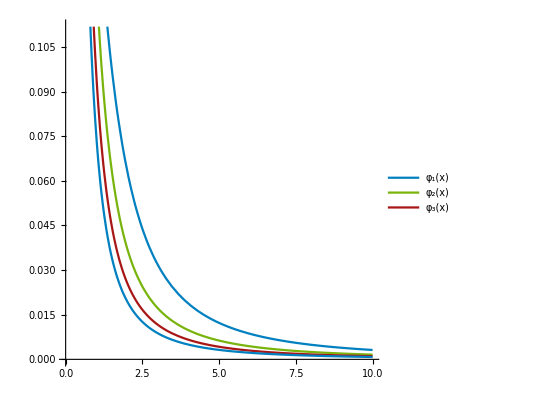

```mathematica
maxX=10
p =Plot[{phi[x,1],phi[x,2],phi[x,3],phi[x,4]},{x,0,maxX},PlotStyle->{RGBColor[0, 0.501961, 0.752941],RGBColor[0.47451, 0.705882, 0.0470588],RGBColor[0.662745, 0.0862745, 0.0862745]},
AspectRatio->1,
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},LabelStyle->(FontFamily->"STIX Two Text"),
PlotLegends->{Subscript[φ,1][x],Subscript[φ,2][x],Subscript[φ,3][x]}]
```

```mathematica
Export["D:\\wolfram\\approx.pdf",p]
```

D:\wolfram\approx.pdf

```mathematica
2 *Pi
```

2 π